## Observers: compare prediction with current designs Chapter 5 (Section 5.4.2 – Direct Digital Design)

```mathematica
Clear["Global`*"];
SetOptions[ListPlot,Joined->True,InterpolationOrder->0,PlotRange -> All];
SetOptions[Plot,PlotRange -> All];
Ts=0.1; tmax=3π;   Nt=Round[tmax/Ts];
```

```mathematica
G0=1/(s^2+1);                                                   (* undamped harmonic oscillator *)
G0tf=TransferFunctionModel[G0,s];   (* transfer function version *)
G0ss=StateSpaceModel[G0tf];                               (* state space version *)
G0dss=ToDiscreteTimeModel[G0ss,Ts,z,Method -> "ZeroOrderHold"];
{a,b,c,d}=Normal[G0dss];                                (* get a,b,c,d matrices *)
estimatorpoles={0.7,0.7};      (* sets estimator convergence rate *)
l=EstimatorGains[G0dss,estimatorpoles,Method->"Ackermann"];
```

Design the prediction and current observers

```mathematica
b0=ArrayFlatten[({{b}, {b}})];           (* same input for system and observer *)
c0=({{1, 0, 0, 0}, {0, 0, 1, 0}}) (* output position and estimate *); d0=ArrayFlatten[({{d}, {d}})] ;

ap0= ArrayFlatten[({{a, 0}, {l.c, a-l.c}})];                   (* prediction observer *)
ac0= ArrayFlatten[({{a, 0}, {l.c.a, a-l.c.a}})];                (* current observer *)

G0pss=StateSpaceModel[{ap0,b0,c0,d0},SamplingPeriod->Ts] (* predict. obs.*);G0css=StateSpaceModel[{ac0,b0,c0,d0},SamplingPeriod->Ts](* current obs.*);
```

Make the outputs

```mathematica
ic={0,0,1,0}   (* initial condition:  (0,0) for sys, (1,0) for observer *);
u = UnitStep[t] (* input to oscillator, a step function *);
uvals=Table[UnitStep[(i-1)*Ts],{i,Nt+1}];
y0=OutputResponse[G0ss,UnitStep[t],{t,0,tmax}] (* continuous sys *);
y0d=OutputResponse[{G0pss,ic},u,{t,0,tmax}][[1]]  (* discrete sys *);
yp0=OutputResponse[{G0pss,ic},u,{t,0,tmax}][[2]]  (* prediction obs *);
yc0=OutputResponse[{G0css,ic},u,{t,0,tmax}][[2]]  (* current obs *);

G0css1=SystemsModelExtract[StateOutputEstimator[G0dss,l],All,{1}];
y0d1=OutputResponse[G0dss,u,{t,0,tmax}][[1]] (* same as y0d... *);
yc1=OutputResponse[{G0css1,{1,0}},{uvals,y0d1}][[1]];
(* should be same as yc0 but differs a bit on initial conditions;  maybe due to the way Mathematica puts together the observer???? *)

G0css2=SystemsModelExtract[StateOutputEstimator[G0dss,l,Method->"PredictionEstimator"],All,{1}];
yc2=OutputResponse[{G0css2,{1,0}},{uvals,y0d1}][[1]];
(* the predictor observer works as expected! *)
```

Graphics routines

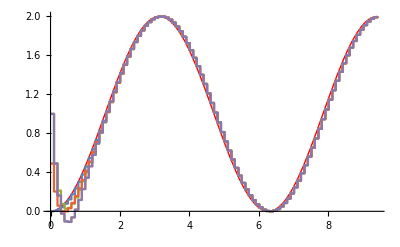

```mathematica
py0=Plot[y0,{t,0,tmax},PlotStyle ->{Thick,Red}];
palld=ListPlot[{y0d,yp0,yc0,yc1,yc2},DataRange->{0,tmax}];
Show[py0,palld]
```

Conclusions:  The current estimator (green curve) tracks the system (blue) better than the prediction estimator (black), which uses observations that are delayed by one time step

State space forms:

```mathematica
{G0css1,G0css2,G0pss,G0css}
```

{0.4049960.09983340.004995830.590008-0.8717270.9950040.09983340.7718930.490.0.0.510.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2121FalseFalseFalseAutomaticNoneAutomatic,0.4850040.09983340.004995830.51-0.9267730.9950040.09983340.8269410000.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2121FalseFalseFalseAutomaticNoneAutomatic,0.9950040.0998334000.00499583-0.09983340.995004000.09983340.510.0.4850040.09983340.004995830.826940.-0.9267730.9950040.099833410000001000.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1241FalseFalseFalseAutomaticNoneAutomatic,0.9950040.0998334000.00499583-0.09983340.995004000.09983340.5074520.0509150.4875520.04891840.004995830.8228080.0825562-0.9226420.9124480.099833410000001000.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1241FalseFalseFalseAutomaticNoneAutomatic}